```mathematica
functionSolve2[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_]:=Module[{solutions,seeds,sol,fulsoly,fulsolz,dsoly,dsolz,sol2,times,ys,tf,tDeU,yDeU,zDeU,yPDeU,zPDeU,yfU,period,Δz,ΔzP,Δt,steplength,speedND,stepfreq,ke,dke,pe,dpe,totalsynctime,percentCong},
period=4Pi;
solutions={};
seeds=Table[i,{i,tDe+0.2,tDe+period,0.25}];
leq[t]=l0-ldev Cos[(t-tDe)];
ltri[t]=Sqrt[(y[t]-yf)^2+(z[t])^2];
fk[t]=(leq[t]-ltri[t]);

sol=NDSolve[{ y''[t]==ϕ^2(fk[t])(y[t]-yf)/(ltri[t]),
z''[t]==ϕ^2((fk[t])(z[t])/(ltri[t]))-γ
,y[tDe]==yDe,y'[tDe]==yPDe,z[tDe]==zDe,z'[tDe]==zPDe},{y[t],z[t]},{t,tDe,tDe+period}];

fulsoly=(y[t]/.sol)[[1]];
fulsolz=(z[t]/.sol)[[1]];
dsoly=D[fulsoly,t];
dsolz=D[fulsolz,t];

Do[
sol2=Quiet@FindRoot[dsoly==yPDe,{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
];

times=Select[t/.solutions,(tDe+0.2)<#<(tDe+period)&];
ys=Flatten[(dsoly/.t->times)];
tf=Table[(ys[[i]]-yPDe)<10^-6,{i,1,Length[ys]}];


tDeU=Min[DeleteDuplicates[Pick[times,tf]]];
yDeU=(fulsoly/.t->tDeU);
zDeU=(fulsolz/.t->tDeU);
yPDeU=(dsoly/.t->tDeU);
zPDeU=(dsolz/.t->tDeU);
yfU=yDeU+Abs[δy];

Δz=Abs[Abs[zDe]-Abs[zDeU]];
ΔzP=Abs[Abs[zPDe]-Abs[zPDeU]];

Δt=tDeU-tDe;
steplength=yDeU-yDe;
speedND=steplength/Δt;
stepfreq=1/Δt;



{{yfU,yDeU,zDeU,yPDeU,zPDeU,tDeU},{steplength,speedND,stepfreq},{Δz,ΔzP},{tDe,fulsoly,fulsolz,Δt,yf}}

]
```

## Function Poincare

```mathematica
poincareFunc[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_,ϵ_]:=Module[{p1,p2,p3,p4,p5,p6,c1,c2,c3,eg,magEG,alltrue},
p1=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe+ϵ,zDe,yPDe,zPDe,tDe];
p2=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe-ϵ,zDe,yPDe,zPDe,tDe];
p3=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe,zDe+ϵ,yPDe,zPDe,tDe];
p4=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe,zDe-ϵ,yPDe,zPDe,tDe];
p5=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe,zDe,yPDe,zPDe+ϵ,tDe];
p6=functionSolve2[ldev,l0,ϕ,γ,δy,yf,yDe,zDe,yPDe,zPDe-ϵ,tDe];

c1={((p1[[1,2]] -p1[[1,1]] )-(p2[[1,2]] -p2[[1,1]] )),(p1[[1,3]]-p2[[1,3]]),p1[[1,5]]-p2[[1,5]]}/(2 ϵ);
c2={((p3[[1,2]] -p3[[1,1]] )-(p4[[1,2]] -p4[[1,1]] )),(p3[[1,3]]-p4[[1,3]]),p3[[1,5]]-p4[[1,5]]}/(2 ϵ);
c3={((p5[[1,2]] -p5[[1,1]] )-(p6[[1,2]] -p6[[1,1]] )),(p5[[1,3]]-p6[[1,3]]),p5[[1,5]]-p6[[1,5]]}/(2 ϵ);

eg=Eigenvalues[Transpose[{c1,c2,c3}]];
magEG=Table[Norm[eg[[i]]],{i,1,3}];
alltrue=And@@Map[#<1&,magEG];

{alltrue,Max[magEG]}]
```

## FilterpointsFunction

```mathematica
filterPoints[results_,points_]:=Module[{resultsUU,truefalse,trueresults,trueϕγ,pcount,truefalse2,ttff,TTFF},

resultsUU=Quiet[Table[ReplacePart[Quiet[results[[i]]],1->Quiet[Delete[results[[i,1]],4]]],{i,1,Length[results]}]];
truefalse=Table[AllTrue[Flatten[resultsUU[[i]]],NumericQ],{i,1,Length[resultsUU]}];
truefalse2=Table[resultsUU[[i,2]]<1000,{i,1,Length[resultsUU]}];
ttff=Transpose[{truefalse,truefalse2}];
TTFF=AllTrue[#,TrueQ]&/@ttff;
trueresults=Pick[resultsUU,TTFF];
trueϕγ=Pick[points,TTFF];
pcount=Length[trueϕγ];{trueresults,trueϕγ,pcount}]
```

## Analysis

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\ForAntY4.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\ForAntY4points.mx"];
```

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
```

```mathematica
resultsU[[1,1,1]]
```

{26.6268,26.5768,0.804109,0.04,-0.00292754,633.787}

```mathematica
poincare=Table[poincareFunc[1.5,1,ϕγU[[i,1]],ϕγU[[i,2]],-0.05,resultsU[[i,1,1,1]],resultsU[[i,1,1,2]](*yDe*),resultsU[[i,1,1,3]](*zDe*),resultsU[[i,1,1,4]](*yPDe*),resultsU[[i,1,1,5]](*zPDe*),resultsU[[i,1,1,6]],10^-3],{i,1,Length[ϕγU]}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\poincare.mx",poincare]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Code\Feasible Region Charactersitics\poincare.mx

```mathematica
poincare=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\poincare.mx"];
```

```mathematica
trues=Table[First[poincare[[i]]],{i,1,Length[ϕγU]}]/.{True->1,False->0};
pointstrue=MapThread[Append,{ϕγU,trues}];
maxEi=Table[Last[poincare[[i]]],{i,1,Length[ϕγU]}];
pointsmaxEi=MapThread[Append,{ϕγU,maxEi}];
```

```mathematica
side=0.0065;
scale=(Differences[MinMax[Last/@ϕγU]]/Differences[MinMax[First/@ϕγU]])[[1]];
ticksFunc[steplength_,intD_,intU_]:=Module[{ticks,ticks1,mticks},ticks=Table[{i,Round[i,0.01]},{i,Min[steplength],Max[steplength],(Max[steplength]-Min[steplength])/(3-1)}];
ticks1=Join[{{First[ticks][[1]]+intD,Round[First[ticks][[2]],0.01]}},Most[Rest[ticks]],{{Last[ticks][[1]]-intU,Round[Last[ticks][[2]],0.01]}}];
mticks=Table[{i,""},{i,Min[steplength],Max[steplength],(Max[steplength]-Min[steplength])/(13-1)}];{ticks1,mticks} ]

plotfunc[pointsre1_,re1_,ticks_,label_,ytiks_,xtiks_]:=Legended[Show[Graphics[Table[{Directive[Thickness[0.028],ColorData["Rainbow"][Rescale[pointsre1[[i,3]],MinMax[re1]]]],Rectangle[pointsre1[[i]][[;;2]]-{side,side*scale},pointsre1[[i]][[;;2]]+{side,side*scale}]},{i,1,Length[pointsre1]}],Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},AspectRatio->2/3,Axes->False,ImageSize->{340,260},FrameTicks->{{{#,#}&/@ytiks,Automatic},{{#,#}&/@xtiks,Automatic}}],

PlotRange->All

],

BarLegend[{"Rainbow",MinMax[re1]},LegendMarkerSize->110,LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},LegendLabel->label,Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

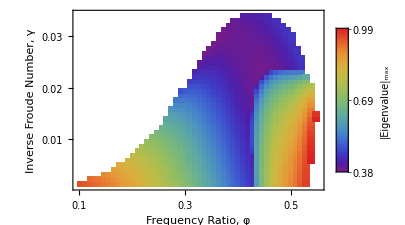

```mathematica
ticks=ticksFunc[maxEi,0.001,0.001];
plot=plotfunc[pointsmaxEi,maxEi,ticks,"|Eigenvalue|_max",{0,0.01,0.02,0.03},{0.1,0.2,0.3,0.4,0.5}]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\poincare.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\poincare.pdf